```mathematica
ClearAll["Global`*"]
```

```mathematica
(*eqnP = (w*bPred1*P*C1 +(1-w)* bPred2*P*C2) - μPred*P/.{bPred1->bPred[M],bPred2->bPred[ϕ*M],μPred->μPred[M]}; (*,σPred->σPred[M],kC->kCons[M],Sub->Sub[M]*)
eqnC1 = λ1*(R/(k/2+R))*C1-( σ1*(1-R/k)+μ1+w*b1*P)*C1/.{k->kRes,λ1->λ[M],μ1->μ[M],σ1->σ[M],b1->b[M]};
eqnC2 = λ2*(R/(k/2+R))*C2-( σ2*(1-R/k)+μ2+(1-w)*b2*P)*C2/.{k->kRes,λ2->λ[ϕ*M],μ2->μ[ϕ*M],σ2->σ[ϕ*M],b2->b[ϕ*M]};
eqnR = α*R*(1-R/(k))-( λ1/Y1*(R/(k/2+R)))*C1-( λ2/Y2*(R/(k/2+R)))*C2/.{k->kRes,λ1->λ[M],Y1->Y[M],λ2->λ[ϕ*M],Y2->Y[ϕ*M]};
LVSS = FullSimplify[Solve[{0==eqnP,0==eqnC1,0==eqnC2,0==eqnR},{P,C1,C2,R}]];
*)
```

```mathematica
(*Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/TwoPreySolutions_predpreyperspectives.m"}],LVSS];*)
```

```mathematica
LVSS = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/TwoPreySolutions_predpreyperspectives.m"}]];
```

```mathematica
Length[LVSS]
```

14

```mathematica
(*Internal Fixed Point*)
Psol = P/.LVSS[[13]]
C1sol = C1/.LVSS[[13]]
C2sol=C2/.LVSS[[13]]
Rsol = R/.LVSS[[13]]
(*Boundary Fixed Points*)
PsolC1only = P/.LVSS[[10]];
C1solC1only = C1/.LVSS[[10]];
C2solC1only=C2/.LVSS[[10]];
RsolC1only = R/.LVSS[[10]];

PsolC2only = P/.LVSS[[12]];
C1solC2only = C1/.LVSS[[12]];
C2solC2only=C2/.LVSS[[12]];
RsolC2only = R/.LVSS[[12]];
```

(kRes (-1+w) b[M ϕ] (-σ[M] (2 λ[M] (λ[M ϕ]-2 μ[M ϕ])+λ[M ϕ] (2 μ[M]+3 σ[M]))+λ[M] (2 λ[M]-2 μ[M]+3 σ[M]) σ[M ϕ])+kRes w b[M] (-2 λ[M ϕ]^2 σ[M]+λ[M] σ[M ϕ] (2 μ[M ϕ]+3 σ[M ϕ])+λ[M ϕ] (2 μ[M ϕ] σ[M]+(2 λ[M]-4 μ[M]-3 σ[M]) σ[M ϕ]))+λ[M ϕ] σ[M] √(kRes^2 (8 ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ]) ((-1+w) b[M ϕ] (μ[M]+σ[M])+w b[M] (μ[M ϕ]+σ[M ϕ]))+((-1+w) b[M ϕ] (2 λ[M]-2 μ[M]-σ[M])-w b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ]))^2))-λ[M] σ[M ϕ] √(kRes^2 (8 ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ]) ((-1+w) b[M ϕ] (μ[M]+σ[M])+w b[M] (μ[M ϕ]+σ[M ϕ]))+((-1+w) b[M ϕ] (2 λ[M]-2 μ[M]-σ[M])-w b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ]))^2)))/(4 kRes ((-1+w) b[M ϕ] λ[M]+w b[M] λ[M ϕ]) ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ]))

(Y[M] ((-1+w)^2 b[M ϕ]^2 (4 λ[M ϕ] μPred[M] σ[M]^2-kRes (-1+w) α bPred[M ϕ] Y[M ϕ] (2 (λ[M]-μ[M])^2-(λ[M]-3 μ[M]) σ[M]))+(-1+w) b[M ϕ] (w b[M] (8 λ[M ϕ] μPred[M] σ[M] σ[M ϕ]+kRes (-1+w) α bPred[M ϕ] Y[M ϕ] (λ[M ϕ] (4 μ[M]+σ[M])-μ[M ϕ] (4 μ[M]+3 σ[M])-3 μ[M] σ[M ϕ]+λ[M] (-4 λ[M ϕ]+4 μ[M ϕ]+σ[M ϕ])))+(-1+w) α bPred[M ϕ] Y[M ϕ] (λ[M]-μ[M]) √(kRes^2 ((-1+w)^2 b[M ϕ]^2 (4 λ[M]^2-4 λ[M] (2 μ[M]+σ[M])+(2 μ[M]+3 σ[M])^2)+2 (-1+w) w b[M] b[M ϕ] (4 (λ[M]-μ[M]) (λ[M ϕ]-μ[M ϕ])-2 (λ[M ϕ]-3 μ[M ϕ]) σ[M]+(-2 λ[M]+6 μ[M]+9 σ[M]) σ[M ϕ])+w^2 b[M]^2 (4 λ[M ϕ]^2-4 λ[M ϕ] (2 μ[M ϕ]+σ[M ϕ])+(2 μ[M ϕ]+3 σ[M ϕ])^2))))+w b[M] (w b[M] (4 λ[M ϕ] μPred[M] σ[M ϕ]^2+kRes (-1+w) α bPred[M ϕ] Y[M ϕ] (-2 (λ[M ϕ]-μ[M ϕ])^2+(λ[M ϕ]-3 μ[M ϕ]) σ[M ϕ]))+(-1+w) α bPred[M ϕ] Y[M ϕ] (λ[M ϕ]-μ[M ϕ]) √(kRes^2 ((-1+w)^2 b[M ϕ]^2 (4 λ[M]^2-4 λ[M] (2 μ[M]+σ[M])+(2 μ[M]+3 σ[M])^2)+2 (-1+w) w b[M] b[M ϕ] (4 (λ[M]-μ[M]) (λ[M ϕ]-μ[M ϕ])-2 (λ[M ϕ]-3 μ[M ϕ]) σ[M]+(-2 λ[M]+6 μ[M]+9 σ[M]) σ[M ϕ])+w^2 b[M]^2 (4 λ[M ϕ]^2-4 λ[M ϕ] (2 μ[M ϕ]+σ[M ϕ])+(2 μ[M ϕ]+3 σ[M ϕ])^2))))))/(4 ((-1+w) bPred[M ϕ] Y[M ϕ] λ[M]+w bPred[M] Y[M] λ[M ϕ]) ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ])^2)

(Y[M ϕ] (-4 λ[M] μPred[M] ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ])^2-w α b[M ϕ] bPred[M] Y[M] λ[M] √(kRes^2 (8 ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ]) ((-1+w) b[M ϕ] (μ[M]+σ[M])+w b[M] (μ[M ϕ]+σ[M ϕ]))+((-1+w) b[M ϕ] (2 λ[M]-2 μ[M]-σ[M])-w b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ]))^2))+w^2 α b[M ϕ] bPred[M] Y[M] λ[M] √(kRes^2 (8 ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ]) ((-1+w) b[M ϕ] (μ[M]+σ[M])+w b[M] (μ[M ϕ]+σ[M ϕ]))+((-1+w) b[M ϕ] (2 λ[M]-2 μ[M]-σ[M])-w b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ]))^2))+w^2 α b[M] bPred[M] Y[M] λ[M ϕ] √(kRes^2 (8 ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ]) ((-1+w) b[M ϕ] (μ[M]+σ[M])+w b[M] (μ[M ϕ]+σ[M ϕ]))+((-1+w) b[M ϕ] (2 λ[M]-2 μ[M]-σ[M])-w b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ]))^2))+w α b[M ϕ] bPred[M] Y[M] μ[M] √(kRes^2 (8 ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ]) ((-1+w) b[M ϕ] (μ[M]+σ[M])+w b[M] (μ[M ϕ]+σ[M ϕ]))+((-1+w) b[M ϕ] (2 λ[M]-2 μ[M]-σ[M])-w b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ]))^2))-w^2 α b[M ϕ] bPred[M] Y[M] μ[M] √(kRes^2 (8 ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ]) ((-1+w) b[M ϕ] (μ[M]+σ[M])+w b[M] (μ[M ϕ]+σ[M ϕ]))+((-1+w) b[M ϕ] (2 λ[M]-2 μ[M]-σ[M])-w b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ]))^2))-w^2 α b[M] bPred[M] Y[M] μ[M ϕ] √(kRes^2 (8 ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ]) ((-1+w) b[M ϕ] (μ[M]+σ[M])+w b[M] (μ[M ϕ]+σ[M ϕ]))+((-1+w) b[M ϕ] (2 λ[M]-2 μ[M]-σ[M])-w b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ]))^2))+kRes w α bPred[M] Y[M] (-(-1+w)^2 b[M ϕ]^2 (2 (λ[M]-μ[M])^2-(λ[M]-3 μ[M]) σ[M])+w^2 b[M]^2 (-2 (λ[M ϕ]-μ[M ϕ])^2+(λ[M ϕ]-3 μ[M ϕ]) σ[M ϕ])+(-1+w) w b[M] b[M ϕ] (λ[M ϕ] (4 μ[M]+σ[M])-μ[M ϕ] (4 μ[M]+3 σ[M])-3 μ[M] σ[M ϕ]+λ[M] (-4 λ[M ϕ]+4 μ[M ϕ]+σ[M ϕ])))))/(4 ((-1+w) bPred[M ϕ] Y[M ϕ] λ[M]+w bPred[M] Y[M] λ[M ϕ]) ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ])^2)

1/(4 (-1+w) b[M ϕ] σ[M]+4 w b[M] σ[M ϕ])(-kRes (-1+w) b[M ϕ] (2 λ[M]-2 μ[M]-σ[M])+kRes w b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ])+√(kRes^2 (8 ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ]) ((-1+w) b[M ϕ] (μ[M]+σ[M])+w b[M] (μ[M ϕ]+σ[M ϕ]))+((-1+w) b[M ϕ] (2 λ[M]-2 μ[M]-σ[M])-w b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ]))^2)))

What are the solutions if the predator is specializing on C1? (w->1)

```mathematica
PsolNoC2= FullSimplify[Psol/.w->1]
C1solNoC2= FullSimplify[C1sol/.w->1]
C2solNoC2= FullSimplify[C2sol/.w->1]
RsolNoC2 = FullSimplify[Rsol/.w->1]
```

1/(4 kRes b[M]^2 λ[M ϕ] σ[M ϕ])((λ[M ϕ] σ[M]-λ[M] σ[M ϕ]) √(kRes^2 b[M]^2 (4 λ[M ϕ]^2-4 λ[M ϕ] (2 μ[M ϕ]+σ[M ϕ])+(2 μ[M ϕ]+3 σ[M ϕ])^2))+kRes b[M] (-2 λ[M ϕ]^2 σ[M]+λ[M] σ[M ϕ] (2 μ[M ϕ]+3 σ[M ϕ])+λ[M ϕ] (2 μ[M ϕ] σ[M]+(2 λ[M]-4 μ[M]-3 σ[M]) σ[M ϕ])))

μPred[M]/bPred[M]

1/(4 b[M] bPred[M] Y[M] λ[M ϕ] σ[M ϕ]^2)Y[M ϕ] (α bPred[M] Y[M] (λ[M ϕ]-μ[M ϕ]) √(kRes^2 b[M]^2 (4 λ[M ϕ]^2-4 λ[M ϕ] (2 μ[M ϕ]+σ[M ϕ])+(2 μ[M ϕ]+3 σ[M ϕ])^2))+b[M] (-4 λ[M] μPred[M] σ[M ϕ]^2+kRes α bPred[M] Y[M] (-2 (λ[M ϕ]-μ[M ϕ])^2+(λ[M ϕ]-3 μ[M ϕ]) σ[M ϕ])))

(kRes b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ])+√(kRes^2 b[M]^2 (8 σ[M ϕ] (μ[M ϕ]+σ[M ϕ])+(-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ])^2)))/(4 b[M] σ[M ϕ])

```mathematica
JacobianFullModel=({
{D[eqnP,P],D[eqnP,C1],D[eqnP,C2],D[eqnP,R]},
{D[eqnC1,P],D[eqnC1,C1],D[eqnC1,C2],D[eqnC1,R]},
{D[eqnC2,P],D[eqnC2,C1],D[eqnC2,C2],D[eqnC2,R]},
{D[eqnR,P],D[eqnR,C1],D[eqnR,C2],D[eqnR,R]}})/.{P->Psol,C1->C1sol,C2->C2sol,R->Rsol};
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/carnivoredensities_trimmed.csv"}],"csv"];
ExpPredfitdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/ExpPred_fit_table_revreps_large.csv"}],"csv"];
ExpPreyfitdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/ExpPrey_fit_table_revreps_large.csv"}],"csv"];
ExpPredmassdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/ExpPredmass_tablereps_large.csv"}],"csv"];
ExpPreymassdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/ExpPreymass_tablereps_large.csv"}],"csv"];
LogitMatrixData = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/logit_matrix_meso.csv"}],"csv"];
kRes=23000;(*grams/m^2 carrying capacity of resource*)

Ed=18200; (*J/g of plant Resource *)
B0=4.7*10^(-2);(*W g^−0.75 for herbivores*)
Em=5774;(*J/gram - energy required to build gram of herbivore*)
a = B0/Em;

(*s=1;*)
Emprime =7000;
aprime =  B0/Emprime;
γ1=1.19;
ζ=1.00;
f0=0.0202;
mm0=0.383;
α=(*2.10*10^(-9)*)(9.45*10^(-9));


τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate of herbivore *)
BLam[M_]:=1/(3 a)ⅇ^(-(a τLam[M])/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam[M])/M^(1/4))) m0[M]+M (-48 ⅇ^((3 a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))-36 ⅇ^((a τLam[M])/(2 M^(1/4))) (-1+(m0[M]/M)^(1/4))^2-16 ⅇ^((a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))^3+3 (-1+4 (m0[M]/M)^(1/4)-6 √(m0[M]/M)+4 (m0[M]/M)^(3/4))+ⅇ^((a τLam[M])/M^(1/4)) (-25+12 (m0[M]/M)^(1/4)+6 √(m0[M]/M)+4 (m0[M]/M)^(3/4)))+3 a ⅇ^((a τLam[M])/M^(1/4)) M^(3/4) τLam[M]);
m0[M_]:=0.097*M^0.92;

(*k=(*10*)23000/2;*)
(*ρ[M_]:=B0*M^(η)/(M*Ed);*)
a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;
μ[M_] := (a0*(Exp[a1*a2*M^(b1+b2)]-1)*M^(b0-b1-b2))/(a1*a2)   (* this is the consumer death rate*)
(*STARVATION MORTALITY*)
ϵsig[M_] := (1-(f0*M^γ1+mm0*M^ζ)/M);(*mortality from starvation state*)
τsig [M_]:=-M^(1/4)/aprime*Log[ϵsig[M]];(*time it takes to go from full to dead*)
σ[M_] := 1/τsig [M];(*starvation mortality rate)*)
η=3/4;
(*B0=4.7*10^(-2);(*W g^−0.75*)*)
B0Pred =(10^0.32)(*kJ/day*)*((0.01157(*Watts*))/(1(*kJ/day*))); (* in (kJ/d) for carnivora from https://doi.org/10.1086/432852 USING LOG10!!!!! *)
EmPred=5774;(*Energy to synthesize a unit of biomass not during starvation J/gram*)

aPred = B0Pred/EmPred;
m0Pred[Mp_]:=0.097*Mp^0.92;
ϵLam = 0.95;
τLamPred[Mp_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0Pred[Mp]/Mp)^(1/4))]*(4*Mp^(1/4))/aPred;
λPred[Mp_]:=(Log[2]/τLamPred[Mp]) (*Fecundity = 2*) 
Bpred[Mp_]:=Integrate[(((1-(1-(m0Pred[Mp]/Mp)^(1/4))*E^(-aPred*t/(4*Mp^(1/4)))))^4)*Mp,{t,0,τLamPred[Mp]}]
PredsperArea[Mp_] :=(0.000862119)*Mp^-0.88; (*Inds/m^2 w/ Mp (grams) From Carbone and Gittleman, Science 2002*)
PredDensity[Mp_] := Mp*PredsperArea[Mp]; (*grams/ind * inds/meter^2 = grams/m^2*)

(*Optimal Predator mass given Prey (M) Mass*)
(*OptPredMass[M_]:=ppmrint*M^ppmrslope;*)

(*A Piecewise function incorporate a) the Cruz/Pires relationship for Prey masses 5-10^4 grams; b) the Hayward relationship fro 10^4-10^7 grams*)
(*breakpoint = 10^4;*)
(*OptPredMass[M_] := Piecewise[{{Exp[3.5]*M,M<breakpoint},{ppmrint*M^ppmrslope,M>=breakpoint}}];*)
```

Calculate the Expected size of a predator given an herbivore consumer of size M

```mathematica
(*Simple Relationship*)
OptPredMass[M_]:=ExpPredint*M^ExpPredslope;
ExpPredslope = (ExpPredfitdata[[3,1]]);
ExpPredint = Exp[(ExpPredfitdata[[2,1]])]*((1/1000)^ExpPredslope)*1000; (*converted from KG to grams*)

(*This is currently in terms of the predator (can be obtained by transforming focal prey), translated to nonfocal prey*)
OptPreyMass[Mp_]:=ExpPreyint*(Mp)^ExpPreyslope;
ExpPreyslope = (ExpPreyfitdata[[3,1]]);
ExpPreyint = Exp[(ExpPreyfitdata[[2,1]])]*((1/1000)^ExpPreyslope)*1000; (*converted from KG to grams*)

(*Integrate over KG mass values, because that is what is used in {alpha,beta,gamma} optimization*)
plink[alpha_,beta_,gamma_,M_,Mp_]:=Exp[alpha+beta*Log[M/Mp]+gamma*Log[M/Mp]^2]/(1+Exp[alpha+beta*Log[M/Mp]+gamma*Log[M/Mp]^2]);
(*ExpPreyMassLogit[logitvec_,Mp_]:=NIntegrate[plink[logitvec[[1]],logitvec[[2]],logitvec[[3]],M,Mp]*M,{M,1000/1000,(10^7)/1000}]/NIntegrate[plink[logitvec[[1]],logitvec[[2]],logitvec[[3]],M,Mp],{M,1000/1000,(10^7)/1000}];*)

ExpPreyMassLogit[logitvec_,PreyMassVec_,Mp_]:=Sum[plink[logitvec[[1]],logitvec[[2]],logitvec[[3]],PreyMassVec[[j]],Mp]*PreyMassVec[[j]],{j,1,Length[PreyMassVec]}]/Sum[plink[logitvec[[1]],logitvec[[2]],logitvec[[3]],PreyMassVec[[j]],Mp],{j,1,Length[PreyMassVec]}];

ExpectedPredMass[logitvec_,PredMassVec_,M_]:=(∑_(j=1)^Length[PredMassVec] plink[logitvec[[1]],logitvec[[2]],logitvec[[3]],M,PredMassVec[[j]]]*PredMassVec[[j]])/(∑_(j=1)^Length[PredMassVec] plink[logitvec[[1]],logitvec[[2]],logitvec[[3]],M,PredMassVec[[j]]]);

(*Species-Specific Logit Vecs*)
ExpectedPredMassSpeciesSpecific[logitmatrix_,PredMassVec_,M_]:=(∑_(j=1)^Length[PredMassVec] plink[logitmatrix[[j,1]],logitmatrix[[j,2]],logitmatrix[[j,3]],M,PredMassVec[[j]]]*PredMassVec[[j]])/(∑_(j=1)^Length[PredMassVec] plink[logitmatrix[[j,1]],logitmatrix[[j,2]],logitmatrix[[j,3]],M,PredMassVec[[j]]]);
(*Complex Relationship -- doesn't work so well*)
(*ExpPredMassGenForm[logitvec_,PredMassMean_,PredMassSD_,M_]:=NIntegrate[plink[logitvec[[1]],logitvec[[2]],logitvec[[3]],M,Mp]*((ⅇ^(-(-PredMassMean+Log[Mp])^2/(2 PredMassSD^2)))/(Mp √(2 π) PredMassSD))*Mp,{Mp,1,10^6}]/NIntegrate[plink[logitvec[[1]],logitvec[[2]],logitvec[[3]],M,Mp]*((ⅇ^(-(-PredMassMean+Log[Mp])^2/(2 PredMassSD^2)))/(Mp √(2 π) PredMassSD)),{Mp,1,10^6}];
PredMassMeso= {5,45,80,250,5000,12500,35000,60000,110000};
alphameso =-1.5;
betameso =-1;
gammameso =-0.12;
logitmeso = {alphameso,betameso,gammameso};
OptPredMass[M_] := Quiet[Evaluate[ExpPredMassGenForm[logitmeso,Log[Mean[PredMassMeso]],(√Log[1/2 ⅇ^(-2 μ) (ⅇ^(2 μ)+√(ⅇ^(4 μ)+4 ⅇ^(2 μ) stdev^2))]/.{μ->Log[Mean[PredMassMeso]],stdev->70000}),M]//Simplify]];*)
```

Import Logit Parameters

```mathematica
PredMassMacro = {93,93,108,317,36,12,1180,2.4,2633,102,6500,4,9,20,3.5,136,3.8,22,0.04,145,309,35};
macroserengetilogitvec={2.0558989052412504,-1.918476481051926,0.047825684997587214};
mesologitvec={-1.5,-1,-0.12};
LogitMatrixMeso = Transpose[{LogitMatrixData[[2;;13,2]],LogitMatrixData[[2;;13,3]],LogitMatrixData[[2;;13,4]]}]
mesogenerallogitvec = {-1.5,-1,-0.12};
mesofelidslogitvec ={-1.12,-1.38,-0.20};(* {-0.84,-0.87,-0.12};*)
mesononfelidslogitvec={-2.84,-0.67,-0.01};
(*{-2.2,-0.67,-0.02};*)
PredMassMeso = {100,51.6,11.9,8.99,3.9,3.249,3.59,2.2,23.2,9.83,5.23,6.949};
PredMassMesoSmilo = {100,51.6,11.9,8.99,3.9,3.249,3.59,2.2,23.2,9.83,5.23,6.949,220};
PredMassMesoFelids = {100,51.6,11.9,8.99,3.9,3.249,3.59,2.2}; (*Smilodon populator=338 (220, 436)*)
PredMassMesoNonFelids = {23.2,9.83,5.23,6.949};
```

{{-2.63935,-3.08932,-0.493212},{-1.13229,-1.28659,-0.225007},{-0.904094,-1.61149,-0.201734},{-2.78341,-1.31059,-0.128346},{-0.179215,-1.18314,-0.220345},{-0.932505,-2.03602,-0.283136},{-0.273401,-1.14947,-0.207688},{-4.50169,-3.11868,-0.39284},{-2.80576,-1.04896,-0.0535284},{-1.54748,-0.989647,-0.112394},{-4.37324,-0.46665,0.0848872},{-5.66363,-0.265945,0.161473}}

```mathematica
(*(Add Smilodon ???)*)
```

Add Smilodon?
Option 1: Same logitvec as P. onca {-2.6,-3.1,-0.49}
Option 2: Serengetic logitvec
Option 3: Artificial logitvec... one that increases its prey size range and mean prey size might be {1, -2.45, -1}
Option 3: Artificial logitvec... If it is mainly eating things much much larger than itself, then {1, 2, -1}

```mathematica
LogitMatrixMesoSmilo = Append[LogitMatrixMeso,{1,-2,-1}];
```

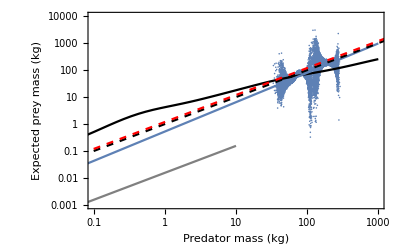

```mathematica
Show[{
ListLogLogPlot[ExpPreymassdata,Frame->True,FrameLabel->{"Predator mass (kg)","Expected prey mass (kg)"},PlotRange->{{0.1,1000},{1/1000,(10^7)/1000}}],
LogLogPlot[ExpPreyMassLogit[macroserengetilogitvec,PredMassMacro,Mp],{Mp,10/1000,(10^6)/1000},PlotStyle->Black],
LogLogPlot[OptPreyMass[Mp]/1000/.Mp->(Mpkg*1000),{Mpkg,(10^1)/1000,(10^6)/1000}],
LogLogPlot[Mp*Exp[-mesologitvec[[2]]/(2*mesologitvec[[3]])],{Mp,(10^1)/1000,10},PlotStyle->Gray],
LogLogPlot[Mp,{Mp,0.1,10^6},PlotStyle->Directive[{Black, Dashed}]], (*1:1*)
LogLogPlot[1.19*Mp,{Mp,0.1,10^6},PlotStyle->Directive[{Red, Dashed}]] (*Carbone 2001*)
}]
```

```mathematica
OptPreyMass[Mp]
```

0.284959 Mp^1.08871

```mathematica
(1/667.47)^(1/(0.4268-1))
```

84621.4

```mathematica
LogitMatrixData[[All,1]]
```

{predator,P. onca,P. concolor,L. pardalis,P. yagouaroundi,L.colocolo,L. wiedii,L.geoffroyi,L. guttulus,C. brachyurus,L. culpaeus,C. thous,P. cancrivorus,General,Felidae,Non-Felidae}

```mathematica
(*ExpectedPredMassMeanMeso[M_] := Mean[{ExpectedPredMass[mesofelidslogitvec,PredMassMesoFelids,M],ExpectedPredMass[mesononfelidslogitvec,PredMassMesoNonFelids,M]}];*)
(*Weighted average by length of Felid/NonFelid categories*)
ExpectedPredMassMeanMeso[M_] := (Length[PredMassMesoFelids]/Length[PredMassMeso])*ExpectedPredMass[mesofelidslogitvec,PredMassMesoFelids,M]+(Length[PredMassMesoNonFelids]/Length[PredMassMeso])*ExpectedPredMass[mesononfelidslogitvec,PredMassMesoNonFelids,M];
```

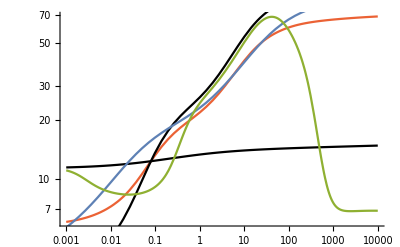

```mathematica
Show[{
LogLogPlot[ExpectedPredMassMeanMeso[M],{M,10^-3,10^4},PlotStyle->ColorData[97,4]],
LogLogPlot[ExpectedPredMass[mesofelidslogitvec,PredMassMesoFelids,M],{M,10^-3,10^4},PlotStyle->Black],
LogLogPlot[ExpectedPredMass[mesononfelidslogitvec,PredMassMesoNonFelids,M],{M,10^-3,10^4},PlotStyle->Black],
LogLogPlot[ExpectedPredMass[mesogenerallogitvec,PredMassMeso,M],{M,10^-3,10^4},PlotStyle->ColorData[97,1]],
LogLogPlot[ExpectedPredMassSpeciesSpecific[LogitMatrixMeso,PredMassMeso,M],{M,10^-3,10^4},PlotStyle->ColorData[97,3]]
}]
```

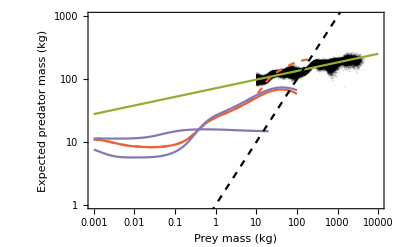

```mathematica
Show[{
ListLogLogPlot[ExpPredmassdata,Frame->True,FrameLabel->{"Prey mass (kg)","Expected predator mass (kg)"},PlotRange->{{10^-3,10^4},{10^0,10^3}},PlotStyle->Directive[{Opacity[0.1],Black}]],
(*LogLogPlot[ExpectedPredMassMeanMeso[M],{M,10^-3,10^4},PlotStyle->Black],*)
(*LogLogPlot[ExpectedPredMass[mesofelidslogitvec,PredMassMesoFelids,M],{M,10^-3,10^4},PlotStyle->Black],
LogLogPlot[ExpectedPredMass[mesononfelidslogitvec,PredMassMesoNonFelids,M],{M,10^-3,10^4},PlotStyle->Black],*)
(*LogLogPlot[ExpectedPredMass[mesogenerallogitvec,PredMassMeso,M],{M,10^-3,200},PlotStyle->ColorData[97,1]],*)
LogLogPlot[ExpectedPredMassSpeciesSpecific[LogitMatrixMeso,PredMassMeso,M],{M,10^-3,100},PlotStyle->ColorData[97,4]],
LogLogPlot[ExpectedPredMassSpeciesSpecific[LogitMatrixMesoSmilo,PredMassMesoSmilo,M],{M,10^-3,200},PlotStyle->Directive[{ColorData[97,4],Dashed}]],

(*Felids*)
LogLogPlot[ExpectedPredMassSpeciesSpecific[LogitMatrixMeso[[1;;8,All]],PredMassMeso[[1;;8]],M],{M,10^-3,100},PlotStyle->Directive[{ColorData[97,5]}]],
(*NonFelids*)
LogLogPlot[ExpectedPredMassSpeciesSpecific[LogitMatrixMeso[[9;;12,All]],PredMassMeso[[9;;12]],M],{M,10^-3,20},PlotStyle->Directive[{ColorData[97,5]}]],
(*ListLogLogPlot[ExpPredMassListMacro,PlotStyle->ColorData[97,4]],
ListLogLogPlot[ExpPredMassListMeso],
ListLogLogPlot[MeanMesoNonFelidsFelids,PlotStyle->ColorData[97,5]],*)
(*ListLogLogPlot[ExpPredMassListMesoFelids],
ListLogLogPlot[ExpPredMassListMesoNonFelids],*)
LogLogPlot[OptPredMass[M]/1000/.M->Mkg*1000,{Mkg,10^-3,10^4},PlotStyle->ColorData[97,3]],
LogLogPlot[M,{M,10^-3,10^4},PlotStyle->Directive[{Black,Dashed}]]
}]
```

Checking conversion from KG to G!

```mathematica
ExpectedPredMassSpeciesSpecificGrams[logitmatrix_,PredMassVec_,M_]:=(1000*((∑_(j=1)^Length[PredMassVec] plink[logitmatrix[[j,1]],logitmatrix[[j,2]],logitmatrix[[j,3]],Mkg,PredMassVec[[j]]]*PredMassVec[[j]])/(∑_(j=1)^Length[PredMassVec] plink[logitmatrix[[j,1]],logitmatrix[[j,2]],logitmatrix[[j,3]],Mkg,PredMassVec[[j]]])))/.Mkg->(M/1000);
```

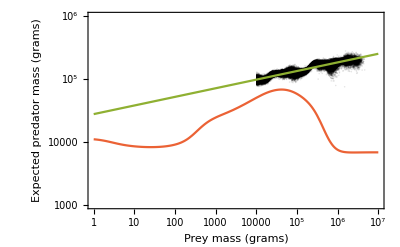

```mathematica
Show[{
ListLogLogPlot[ExpPredmassdata*1000,Frame->True,FrameLabel->{"Prey mass (grams)","Expected predator mass (grams)"},PlotRange->{{1,10^7},{10^3,10^6}},PlotStyle->Directive[{Opacity[0.1],Black}]],
(*LogLogPlot[(1000*ExpectedPredMassSpeciesSpecific[LogitMatrixMeso,PredMassMeso,Mkg])/.Mkg->(M/1000),{M,1,10^7},PlotStyle->ColorData[97,4]],*)
LogLogPlot[ExpectedPredMassSpeciesSpecificGrams[LogitMatrixMeso,PredMassMeso,M],{M,1,10^7},PlotStyle->ColorData[97,4]],
LogLogPlot[OptPredMass[M],{M,1,10^7},PlotStyle->ColorData[97,3]]
}]
```

```mathematica
PredMassMeso[[1;;8]]
PredMassMeso[[9;;12]]
```

{100,51.6,11.9,8.99,3.9,3.249,3.59,2.2}

{23.2,9.83,5.23,6.949}

```mathematica
Exp[-macroserengetilogitvec[[2]]/(2*macroserengetilogitvec[[3]])]
```

5.13607×10^8

```mathematica
Exp[-mesologitvec[[2]]/(2*mesologitvec[[3]])]
```

0.0155039

```mathematica
N[Exp[-4]]
```

0.0183156

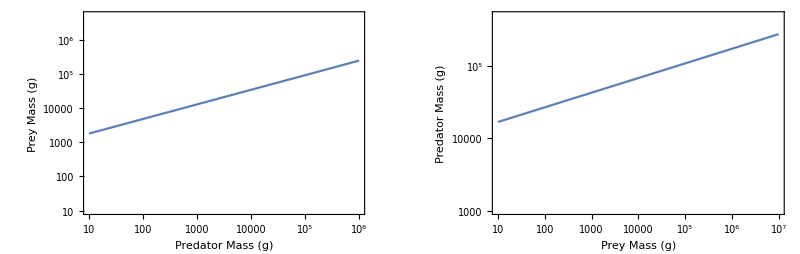

```mathematica
GraphicsRow[{
LogLogPlot[OptPreyMass[M],{M,10^1,10^6},Frame->True,FrameLabel->{"Predator Mass (g)","Prey Mass (g)"},LabelStyle->Directive[FontSize->16],PlotRange->{10,5*10^6}],
LogLogPlot[OptPredMass[M],{M,10^1,10^7},Frame->True,FrameLabel->{"Prey Mass (g)","Predator Mass (g)"},LabelStyle->Directive[FontSize->16],PlotRange->{10^3,5*10^5}]
}]
```

```mathematica
(*DEMO: Given a focal prey of mass 10^5, it's expected predator will be*)
ExpPredofFocalPrey = OptPredMass[10^7]
(*However, that predator's expected prey will be smaller, at*)
ExpPreyofPred = OptPreyMass[ExpPredofFocalPrey]
```

277247.

140481.

Given the mass of a focal herbivore (M, x-axis), what is the size of the preferred prey of the focal prey’s predator (y-axis)?
For smaller focal herbivores, the preferred mass of its most likely predator tends to be larger...
For larger focal herbivores, the preferred mass of its most likely predator tends to be smaller

```mathematica
SecondaryHerbivoreMass = FullSimplify[OptPreyMass[ OptPredMass[M]]]
```

34842.6 M^0.0865009

```mathematica
MinMC1 = M/.Solve[OptPredMass[M]==10000,M][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.759118

```mathematica
OptPreyMass[OptPredMass[MinMC1]]
```

34021.8

This means a roughly 1 gram mammal has an expected predator that is 10 Kg...
But that 10 Kg predator is really focusing on 34 kg prey

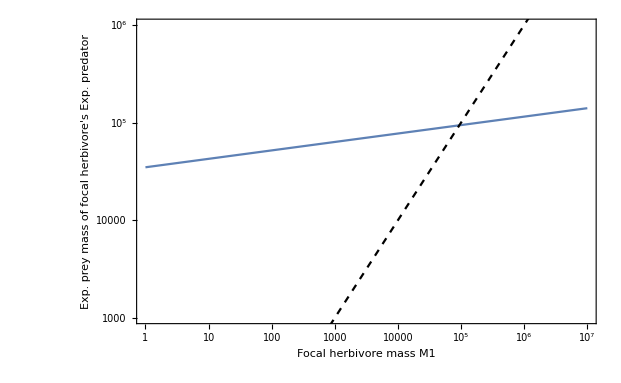

```mathematica
Show[{
LogLogPlot[OptPreyMass[ OptPredMass[M]],{M,1,10^7},PlotRange->{10^3,10^6},Frame->True,FrameLabel->{"Focal herbivore mass M1","Exp. prey mass of focal herbivore's Exp. predator"},LabelStyle->Directive[FontSize->16]],
LogLogPlot[M,{M,1,10^7},PlotStyle->Directive[{Black,Dashed}]]
}]
```

Where does this line meet the 1:1?

```mathematica
ExpMC2 = OptPreyMass[OptPredMass[M]]
ExpMC2Exponent = Exponent[ExpMC2,M];
ExpMC2Coefficient = ExpMC2/M^Exponent[ExpMC2,M];
MCross = (1/ExpMC2Coefficient)^(1/(ExpMC2Exponent-1))
```

34842.6 M^0.0865009

93801.9

Show the inputted PPMR

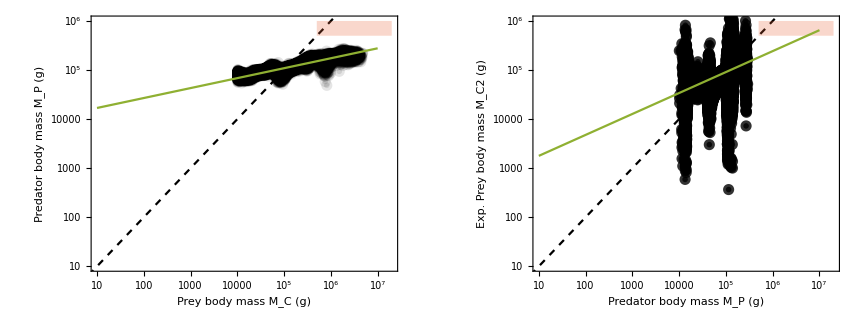

```mathematica
(*nlm = NonlinearModelFit[predpreymassdata*1000,nlm1*x^(nlm2),{nlm1,nlm2},x,MaxIterations->1000];
lm =LinearModelFit[Log@(predpreymassdata*1000),x,x];
lmparams=lm["BestFitParameters"];
nlmconfint=nlm["ParameterConfidenceIntervals",ConfidenceLevel->0.95];*)
pstyleherb=Graphics[{EdgeForm[{Black,Thickness[0.2],Opacity[0.2]}],Opacity[0.1],FaceForm[Black],Disk[]}];
pstyleherbExpPrey=Graphics[{EdgeForm[{Black,Thickness[0.2],Opacity[0.2]}],Opacity[0.8],FaceForm[Black],Disk[]}];
PPMRPlotNLM = 
GraphicsRow[{
Show[{
ListLogLogPlot[ExpPredmassdata*1000,Frame->True,FrameLabel->{"Prey body mass M_C (g)","Predator body mass M_P (g)"},LabelStyle->Directive[FontSize->16],ImageSize->500,AspectRatio->3/4,PlotMarkers->{pstyleherb,.010},PlotRange->{{10^1,2*10^7},{10^1,10^6}}],
LogLogPlot[M,{M,1,2*10^7},PlotStyle->Directive[Dashed,Black]],
(*LogLogPlot[nlm[x],{x,100,5000}],*)
(*LogLogPlot[nlm[x],{x,100000,3200000},PlotStyle->Directive[Black,Thickness[0.008]]],
LogLogPlot[{nlmconfint[[1,1]]*x^(nlmconfint[[2,1]]),nlmconfint[[1,2]]*x^(nlmconfint[[2,2]])},{x,10^1,3200000},PlotStyle->Transparent,Filling->{1->{2}},FillingStyle->Directive[Green,Opacity[0.25]]],*)
(*ListLogLogPlot[predpreymassdata*1000,PlotStyle->Black],*)
(*LogLogPlot[Exp[lmparams[[1]]]*x^(lmparams[[2]]),{x,10^1,3200000},PlotStyle->ColorData[93,4]],*)
Graphics[{ColorData[97,4],Opacity[0.25],Rectangle[{Log@(5*10^5),Log@(5*10^5)},{Log@(2*10^7),Log@(1*10^6)}]}],
(*Graphics[Text[Style["Megatrophic range",FontSize->16,Black],{Log@(1*10^6),Log@(5*10^(5.5))},Automatic]],*)
(*LogLogPlot[Exp[4]*M,{M,5,1.1*10^5},PlotStyle->ColorData[97,5]] (*Mathias general relationaship*),
LogLogPlot[Exp[3]*M,{M,5,1.1*10^5},PlotStyle->Directive[{ColorData[97,5],Dashed}]] (*Mathias felids relationaship*),*)
LogLogPlot[OptPredMass[M],{M,10^1,10^7},Frame->True,FrameLabel->{"Prey Mass (g)","Predator Mass (g)"},LabelStyle->Directive[FontSize->16],PlotStyle->ColorData[97,3]]
},ImageSize->400,AspectRatio->3/4],

Show[{
ListLogLogPlot[ExpPreymassdata*1000,Frame->True,FrameLabel->{"Predator body mass M_P (g)","Exp. Prey body mass M_C2 (g)"},LabelStyle->Directive[FontSize->16],ImageSize->500,AspectRatio->3/4,PlotMarkers->{pstyleherbExpPrey,.010},PlotRange->{{10^1,2*10^7},{10^1,10^6}}],
LogLogPlot[Mp,{Mp,1,2*10^7},PlotStyle->Directive[Dashed,Black]],
(*LogLogPlot[nlm[x],{x,100,5000}],*)
(*LogLogPlot[nlm[x],{x,100000,3200000},PlotStyle->Directive[Black,Thickness[0.008]]],
LogLogPlot[{nlmconfint[[1,1]]*x^(nlmconfint[[2,1]]),nlmconfint[[1,2]]*x^(nlmconfint[[2,2]])},{x,10^1,3200000},PlotStyle->Transparent,Filling->{1->{2}},FillingStyle->Directive[Green,Opacity[0.25]]],*)
(*ListLogLogPlot[predpreymassdata*1000,PlotStyle->Black],*)
(*LogLogPlot[Exp[lmparams[[1]]]*x^(lmparams[[2]]),{x,10^1,3200000},PlotStyle->ColorData[93,4]],*)
Graphics[{ColorData[97,4],Opacity[0.25],Rectangle[{Log@(5*10^5),Log@(5*10^5)},{Log@(2*10^7),Log@(1*10^6)}]}],
(*Graphics[Text[Style["Megatrophic range",FontSize->16,Black],{Log@(1*10^6),Log@(5*10^(5.5))},Automatic]],*)
(*LogLogPlot[Exp[4]*M,{M,5,1.1*10^5},PlotStyle->ColorData[97,5]] (*Mathias general relationaship*),
LogLogPlot[Exp[3]*M,{M,5,1.1*10^5},PlotStyle->Directive[{ColorData[97,5],Dashed}]] (*Mathias felids relationaship*),*)
LogLogPlot[OptPreyMass[Mp],{Mp,10^1,10^7},Frame->True,PlotStyle->ColorData[97,3]]
},ImageSize->400,AspectRatio->3/4]
}]
```

```mathematica
(*OptPreypermeter2[Mp_] := 0.1156*OptPreyMass[Mp]^-0.77;
(*Damuth: Average Individuals/m2*)
OptPreygramspermeter2[Mp_] :=OptPreypermeter2[Mp]*OptPreyMass[Mp] ;*)
(*Average Individuals/m2 * average grams/individual*)
(*Percent fat + muscle*)
(*percentconsumable[M_]:=( 0.02*M^1.19 + 0.38*M^1.00)/M;*)
(*Or 1 - percent skeletal*)
massSkeletalgrams[M_]:= 0.0335*M^1.09263;
massFatgrams[M_]:=0.02*M^1.19;
massMusclegrams[M_]:=0.38*M^1.0;
massOthergrams[M_]:=M-(massSkeletalgrams[M]+massFatgrams[M]+massMusclegrams[M]);
(*This is nearly 100% from Prange et al. AmNat 1979*)
(*Energy Density of PREY Joules/gram*)
(*BLUBBER energy content 37670 J/gram SAME AS FAT *)
(*NOTE: THINK CAREFULLY ABOUT THIS *)
FatJperG = 37700;
ProteinJperG = 17900;
MuscleJperG = 0.4*ProteinJperG + 0.6*FatJperG;
(*TissueJperG = ProteinJperG+FatJperG;
PercentFat =(FatJperG/TissueJperG);
PercentProtein =(1- PercentFat);*)
Eprey[M_]:=(1/(M))*(massFatgrams[M]*FatJperG+massMusclegrams[M]*MuscleJperG+massOthergrams[M]*MuscleJperG);
(*Eprey[M_,ϵEprey_] := ((PercentProtein*TissueJperG)+(PercentFat*TissueJperG)+0)*(1+ϵEprey)*percentconsumable[M];*)
(*Joules/gram: 17000 protein + 37000 fat + 0 carb per gram of meat http://www.fao.org/3/y5022e/y5022e04.htm  Modified from Merrill and Watt (1973).*)
(*Results of MAXSIZE are very sensitive to Energy Density of Prey*)
YHerbperRes[M_]:=M*Ed/BLam[M]; (*Grams herb / Grams Resource given the mass of an Herbivore*)
Y[M_]:=YHerbperRes[M];
(*kprey[Mp_]:=OptPreygramspermeter2[Mp]; *)(*PREY carrying capacity grams/m^2*)
Ypred[Mp_,M_] := (Mp*Eprey[M])/Bpred[Mp]; (*Grams of predator per grams of prey*)
PreyDensityTheoreticalMax[M_] :=  Evaluate[YHerbperRes[M]*kRes//Simplify]; 
(*PredatorDensityTheoreticalMax[Mp_,M_]:= Evaluate[Ypred[Mp,M]*YHerbperRes[M]*kRes//Simplify]; *)
PredatorDensityTheoreticalMax[Mp_,M_]:= Evaluate[(*(1/2)**)(Ypred[Mp,M]*YHerbperRes[M]*kRes+Ypred[Mp,ϕ*M]*YHerbperRes[ϕ*M]*kRes)//Simplify]; 
predgrowthrateperconsumer[Mp_,M_] :=λPred[Mp]/PreyDensityTheoreticalMax[M];
(*predatedconsumerdensity[Mp_,M_]:=PredDensity[Mp]/Ypred[Mp,M];*)
(*predatedconsumerdensity[Mp_,M_]:=1/Ypred[Mp,M];*)
(*predrate[Mp_,M_,ϵEprey_] := (λPred[Mp]*PredDensity[Mp])/PredDensityMaxPreyGrowth[Mp,M,ϵEprey](*((1/time)*gpred/m^2)/(gpred/m^2)=1/time*);*)
predmortality = FullSimplify[predgrowthrateperconsumer[Mp,M]*1/Ypred[Mp,M]];
predmortalityfull[Mp_,M_]:=  Evaluate[predmortality//Simplify];
b[M_] :=predmortalityfull[OptPredMass[M],M];

predgrowth =  FullSimplify[predgrowthrateperconsumer[Mp,M]]; (*predatedconsumerdensity without the 1/Yield*)
predgrowthfull[Mp_,M_]:=Evaluate[predgrowth//Simplify];
bPred[M_]:=predgrowthfull[OptPredMass[M],M];
(*bPred[M_]:=λPred[OptPredMass[M]];*)
bPredSub[M_]:=predgrowthfull[OptPredMass[M],M];
(*bPredSub[M_]:=Sub*λPred[OptPredMass[M]];*)



(*Predator starvation*)
σPred[M_]:=(1/τsig [OptPredMass[M]]);
kCons[M_]:=PreyDensityTheoreticalMax[M]; (*Consumer theroetical maximum*)
(*Predator mortality*)
μPred[M_] := (a0*(Exp[a1*a2*OptPredMass[M]^(b1+b2)]-1)*OptPredMass[M]^(b0-b1-b2))/(a1*a2);   (* this is the consumer death rate*)
(*Subsidies could be set as mass dependent or mass-independent*)
(*Sub[M_]:=CsolNoSubsidies;*)
```

This is the value of ϕ given the mass of the focal consumer MC1

```mathematica
phiscaling[M_] := FullSimplify[OptPreyMass[OptPredMass[M]]/M]
```

```mathematica
C2Table = Table[({M,phiscaling[M]*M,((1/M)*C2sol)}/.{ϕ->phiscaling[M],w->0.3})/.M->10^i,{i,0,7,0.1}];
C2TableM = Transpose[{C2Table[[All,1]],C2Table[[All,3]]}];
C2TableM2 = Transpose[{C2Table[[All,2]],C2Table[[All,3]]}];
```

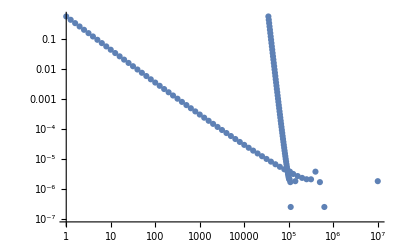

```mathematica
Show[{
(*ListLogLogPlot[C2TableM],*)
ListLogLogPlot[C2TableM2,PlotRange->{{1,10^7},All}],
ListLogLogPlot[C2TableM]
}]
```

```mathematica
PercentGrowthConsumer1=0.9; (*Percent with which the predator relies on Consumer 1 for food*)
(*ScaledMassConsumer2 =0.9; (*Proportional size of Consumer 2 with respect to Consumer 1 (focal)*)*)

Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,10}},Frame->True,FrameLabel->{"Body mass of consumers (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*C1sol/.{w->PercentGrowthConsumer1,ϕ->phiscaling[M]},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]],
(*LogLogPlot[(((1/(ϕ*M))*C2sol)/.{M->M2/ϕ})/.{w->PercentGrowthConsumer1,ϕ->phiscaling[M]},{M2,1,10^8},Frame->True,PlotStyle->ColorData[97,3]],*)
ListLogLogPlot[C2Table[[All,2;;3]],Joined->True,PlotStyle->ColorData[97,3]],
LogLogPlot[(1/OptPredMass[M])*Psol/.{w->PercentGrowthConsumer1,ϕ->phiscaling[M]},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,4]]
}]
```